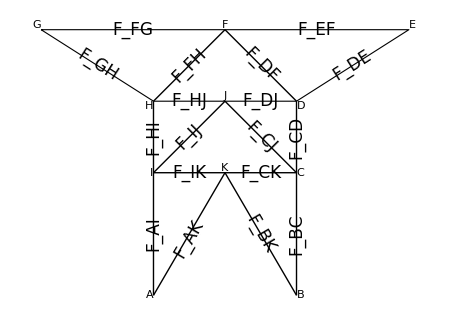

```mathematica
Module[{w1,w2,h1,h2,θ1,θ2,θ3},
w1=7;w2=11;h1=7;h2=12;
θ1=ArcTan[h2/w1];θ2=ArcTan[h1/w2];θ3=ArcTan[h1/w1];

Graphics[{
{EdgeForm@Thick,FaceForm@None,Polygon[{{-w1-w2,2*h1+h2},{w1+w2,2*h1+h2},{w1,h1+h2},{-w1,h1+h2}}]},
{Thick,{Line[{{#*w1,h1+h2},{0,2*h1+h2}}],Line[{{#*w1,h2},{0,h1+h2}}],Line[{{#*w1,0},{0,h2}}]}&/@{-1,1},
Line[{{#,h1+h2},{#,0}}]&/@{-w1,w1},
Line[{{-w1,h2},{w1,h2}}]},

Text[Framed[Style[Row@{" ",#1," "},15],RoundingRadius->15],#2,#3]&@@@{{"A",{-w1,0},{1.5,0}},{"B",{w1,0},{-1.5,0}},{"C",{w1,h2},{-1.5,0}},{"D",{w1,h1+h2},{-1.5,1}},{"E",{w1+w2,2*h1+h2},{-1,-1}},{"F",{0,2*h1+h2},{0,-1.5}},{"G",{-w1-w2,2*h1+h2},{1,-1}},{"H",{-w1,h1+h2},{1.5,1}},{" I ",{-w1,h2},{1.5,0}},{"J",{0,h1+h2},{0,-1.5}},{"K",{0,h2},{0,-1.5}}},

(*Text[Rotate[Style[Row@{" ",Subscript[Style["F",Italic],#1]," "},17,Background->White],#3],#2]&@@@{{"1,AI",{-w1,h2/2},π/2},{"6,HI",{-w1,h2+h1/2},π/2},{"3,GH",{-w1-w2/2,1.5*h1+h2},-θ2},{"3,FG",{-(w1+w2)/2,2*h1+h2},0},{"4,EF",{(w1+w2)/2,2*h1+h2},0},{"4,DE",{w1+0.5*w2,1.5*h1+h2},θ2},{"7,CD",{w1,0.5*h1+h2},π/2},{"2,BC",{w1,0.5h2},π/2},{"2,BK",{0.5*w1,h2/2},-θ1},{"1,AK",{-0.5*w1,0.5*w2},θ1},{"9,IK",{-0.5*w1,h2},0},{"9,IJ",{-0.5*w1,0.5*h1+h2},θ3},{"6,HJ",{-0.5*w1,h1+h2},0},{"5,FH",{-0.5*w1,1.5*h1+h2},θ3},{"5,DF",{0.5*w1,1.5*h1+h2},-θ3},{"7,DJ",{0.5*w1,h1+h2},0},{"8,CJ",{0.5*w1,0.5*h1+h2},-θ3},{"8,CK",{0.5*w1,h2},0}}*)
Text[Rotate[Style[Row@{" ",Subscript[Style["F",Italic],#1]," "},17,Background->White],#3],#2]&@@@{{"AI",{-w1,h2/2},π/2},{"HI",{-w1,h2+h1/2},π/2},{"GH",{-w1-w2/2,1.5*h1+h2},-θ2},{"FG",{-(w1+w2)/2,2*h1+h2},0},{"EF",{(w1+w2)/2,2*h1+h2},0},{"DE",{w1+0.5*w2,1.5*h1+h2},θ2},{"CD",{w1,0.5*h1+h2},π/2},{"BC",{w1,0.5h2},π/2},{"BK",{0.5*w1,h2/2},-θ1},{"AK",{-0.5*w1,0.5*w2},θ1},{"IK",{-0.5*w1,h2},0},{"IJ",{-0.5*w1,0.5*h1+h2},θ3},{"HJ",{-0.5*w1,h1+h2},0},{"FH",{-0.5*w1,1.5*h1+h2},θ3},{"DF",{0.5*w1,1.5*h1+h2},-θ3},{"DJ",{0.5*w1,h1+h2},0},{"CJ",{0.5*w1,0.5*h1+h2},-θ3},{"CK",{0.5*w1,h2},0}}
},ImageSize->450]
]
```

```mathematica
Manipulate[
Module[{w1,w2,h1,h2,θ1,θ2,θ3,sol,RAx,RAy,RB,scale,colC,colT},
w1=7;w2=11;h1=7;h2=12;
θ1=ArcTan[h2/w1];θ2=ArcTan[h1/w2];θ3=ArcTan[h1/w1];

sol=Quiet@Solve[{rax+FEx==0,
w2*ray+(2*w1+w2)*rb+2*(w1+w2)*(-FEy)==0,ray+rb-FG-FEy==0},{rax,ray,rb}][[1]];
RAx=rax/.sol;RAy=ray/.sol;RB=rb/.sol;

scale[F_]:=3+10*Rescale[Abs@F,{0,25.7}];
colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];

Graphics[{Thick,Arrowheads@0.04,
Arrow[{{-(w1+w2),2*h1+h2},{-(w1+w2),2*h1+h2-scale[FG]}}],
Arrow[{{w1+w2,2*h1+h2},{w1+w2,2*h1+h2-scale[FEy]}}],
If[FEx≠0,Arrow[{{w1+w2,2*h1+h2},{w1+w2+scale[FEx],2*h1+h2}}]],
Arrow[If[RAy<0,Reverse,N]@{{-w1,-0.75-scale[RAy]},{-w1,0}}],If[FEx≠0,Arrow[{{-w1+scale[RAx],0},{-w1,0}}]],
Arrow[{{w1,-0.75-scale[RB]},{w1,0}}],

Text[Style[Subscript[Style["F",Italic],#1],18],#2,#3]&@@@{{"G",{-w1-w2,2*h1+h2-scale[FG]},{0,1.5}},{Row@{"E,",Style["y",Italic]},{w1+w2,2*h1+h2-scale[FEy]},{0,1.5}},If[FEx≠0,{Row@{"E,",Style["x",Italic]},{w1+w2+scale[FEx],2*h1+h2},{-1.2,0}}]},
Text[Style[Subscript[Style["R",Italic],Row@{"A,",Style[#1,Italic]}],18],#2,#3]&@@@{
If[RAx≠0,{"x",{-w1+scale[RAx],0},{-1.2,0}}],{"y",{-w1,-scale[RAy]},{0,2}}},
Text[Style[Subscript[Style["R",Italic],"B"],18],{w1,-scale[RB]},{0,2}],

{colC,Arrowheads@{-0.04,0.04},Arrow[{{-w1,0},{-w1,h2}}],Arrow[{{-w1,h2},{-w1,h1+h2}}],Arrow[{{-w1,h1+h2},{-w1-w2,2*h1+h2}}],Arrow[{{-w1,h2},{0,h2}}],Arrow[{{-w1,h2},{0,h2}}],Arrow[{{0,h1+h2},{w1,h2}}],Arrow[{{-w1,h1+h2},{0,h1+h2}}],Arrow[{{0,h1+h2},{w1,h1+h2}}],Arrow[{{w1,h2},{w1,h1+h2}}],Arrow[{{w1,0},{w1,h2}}],Arrow[{{w1,h1+h2},{w1+w2,2*h1+h2}}],Arrow[{{0,2*h1+h2},{w1,h1+h2}}]},

{colT,Arrowheads@{{0.04,0.315},{-0.04,0.675}},Arrow[{{-w1,0},{0,h2}}],Arrow[{{-w1,h2},{0,h1+h2}}],Arrow[{{0,h2},{w1,h2}}],Arrow[{{-w1,h1+h2},{0,2*h1+h2}}],Arrow[{{-w1-w2,2*h1+h2},{0,2*h1+h2}}],Arrow[{{0,2*h1+h2},{w1+w2,2*h1+h2}}]},

Line[{{0,h2},{w1,0}}],

Text[Framed[Style[Row@{" ",#1," "},15],RoundingRadius->20],#2,#3]&@@@{{"A",{-w1,0},{1.5,-0.5}},{"B",{w1,0},{-1.5,-0.5}},{"C",{w1,h2},{-1.5,0}},{"D",{w1,h1+h2},{-1.5,1}},{"E",{w1+w2,2*h1+h2},{-1,-1.2}},{"F",{0,2*h1+h2},{0,-1.2}},{"G",{-w1-w2,2*h1+h2},{1,-1.2}},{"H",{-w1,h1+h2},{1.5,1}},{" I ",{-w1,h2},{1.5,0}},{"J",{0,h1+h2},{0,-1.2}},{"K",{0,h2},{0,-1.2}}},

Text[Rotate[Framed[Style[Subscript[Style["F",Italic],#1],18],Background->White,FrameStyle->None,FrameMargins->Tiny],0],#2]&@@@{{"1,AI",{-w1,h2/2},π/2},{"2,HI",{-w1,h2+h1/2},π/2},{"3,GH",{-w1-w2/2,1.5*h1+h2},-θ2},{"4,FG",{-(w1+w2)/2,2*h1+h2},0},{"5,EF",{(w1+w2)/2,2*h1+h2},0},{"6,DE",{w1+0.5*w2,1.5*h1+h2},θ2},{"7,CD",{w1,0.5*h1+h2},π/2},{"8,BC",{w1,0.5h2},π/2},{"9,BK",{0.5*w1,h2/2},-θ1},{"10,AK",{-0.5*w1,0.5*w2},θ1},{"11,IK",{-0.5*w1,h2},0},{"12,IJ",{-0.5*w1,0.5*h1+h2},θ3},{"13,HJ",{-0.5*w1,h1+h2},0},{"14,FH",{-0.5*w1,1.5*h1+h2},θ3},{"15,DF",{0.5*w1,1.5*h1+h2},-θ3},{"16,DJ",{0.5*w1,h1+h2},0},{"17CJ",{0.5*w1,0.5*h1+h2},-θ3},{"18,CK",{0.5*w1,h2},0}}
},ImageSize->600]
],
Grid[{
{"forces at joint E (kN)",
Control[{{FEx,1.8,Row@{"horizontal ",Subscript[Style["F",Italic],Row@{"E,",Style["x",Italic]}]}},0,4,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{FEy,8,Row@{"vertical ",Subscript[Style["F",Italic],Row@{"E,",Style["y",Italic]}]}},4,10,0.1,Appearance->"Labeled",ImageSize->Small}]},
{Control[{{FG,5,"force at joint G (kN)"},4,10,0.1,Appearance->"Labeled"}],SpanFromLeft}
},Alignment->Left]
]
```